-Graphics3D-

-Graphics3D-

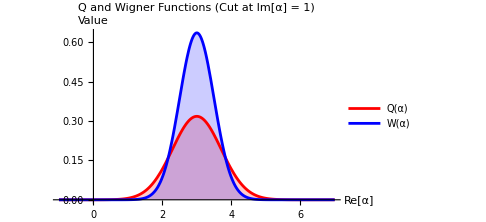

```mathematica
(*Definition of complex variables:α_0 is the state amplitude and α is the phase space coordinate*)(*1. Define complex amplitude for coherent state (e.g.,α_0=3+1i)*)Alpha0=3+I;
ReAlpha0=Re[Alpha0];
ImAlpha0=Im[Alpha0];

(*2. Define phase space distance|α-α_0|^2 in terms of real and imaginary coordinates (x and y)*)
PhaseSpaceDistanceSquared[x_,y_]:=(x-ReAlpha0)^2+(y-ImAlpha0)^2

(*--------------------------------------------------------*)
(*Definition of quasi-probability functions Q and W for coherent state*)

(*Q function (Husimi) for coherent state*)
QFunctionCoherent[x_,y_]:=(1/Pi)*Exp[-PhaseSpaceDistanceSquared[x,y]]

(*Wigner function for coherent state*)
WignerFunctionCoherent[x_,y_]:=(2/Pi)*Exp[-2*PhaseSpaceDistanceSquared[x,y]]

(*--------------------------------------------------------*)
(*a) Plot Q function for coherent state*)

Plot3D[QFunctionCoherent[x,y],{x,-1,7},{y,-3,5},PlotRange->All,ColorFunction->"SolarColors",Mesh->None,AxesLabel->{"Re[α]","Im[α]","Q(α)"},PlotLabel->Style["Q Function for Coherent State |α_0⟩, where α_0 = 3 + i",Bold,14],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*b) Plot Wigner function for coherent state*)

Plot3D[WignerFunctionCoherent[x,y],{x,-1,7},{y,-3,5},PlotRange->All,ColorFunction->"SolarColors",Mesh->None,AxesLabel->{"Re[α]","Im[α]","W(α)"},PlotLabel->Style["Wigner Function for Coherent State |α_0⟩, where α_0 = 3 + i",Bold,14],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*c) Compare function widths along the cut (y=Im(Alpha0))*)

Plot[{QFunctionCoherent[x,ImAlpha0],WignerFunctionCoherent[x,ImAlpha0]},{x,-1,7},PlotLabel->Style["Q and Wigner Functions (Cut at Im[α] = 1)",Bold,14],PlotLegends->{"Q(α)","W(α)"},AxesLabel->{"Re[α]","Value"},Filling->{1->Axis,2->Axis},ImageSize->Medium,PlotStyle->{Red,Blue}]
```